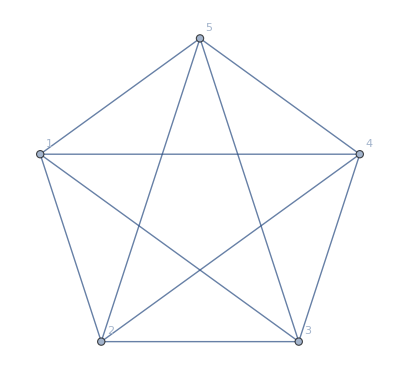

```mathematica
g=CompleteGraph[5,VertexLabels->"Name"]
```

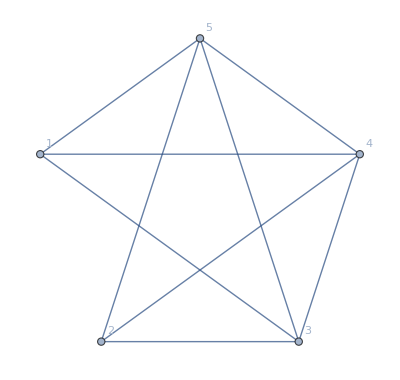
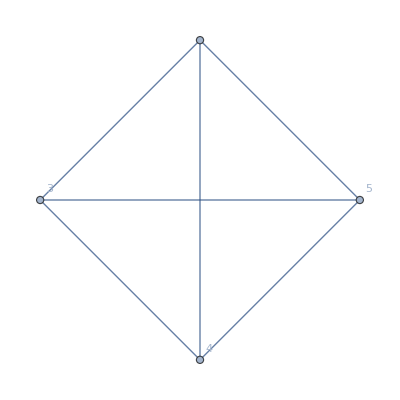

```mathematica
With[{e=UndirectedEdge[1,2]},{g2=EdgeDelete[g,e],EdgeContract[g,e]}]
```

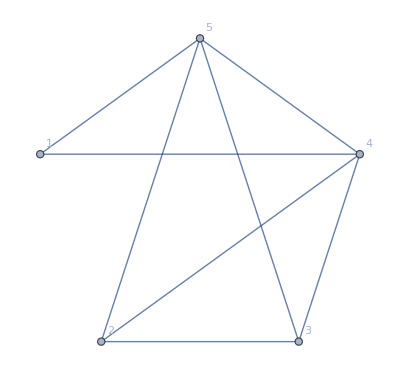
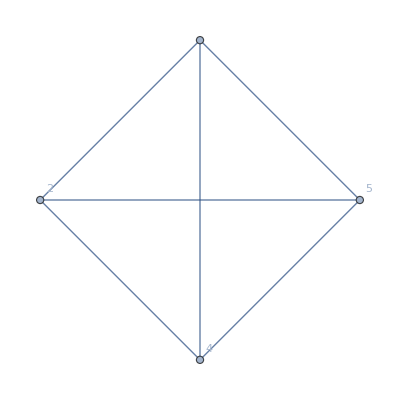

```mathematica
With[{e=UndirectedEdge[1,3]},{g3=EdgeDelete[g2,e],EdgeContract[g2,e]}]
```

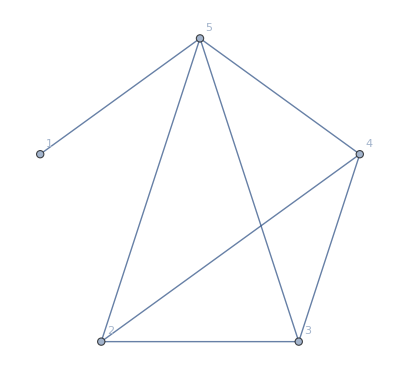
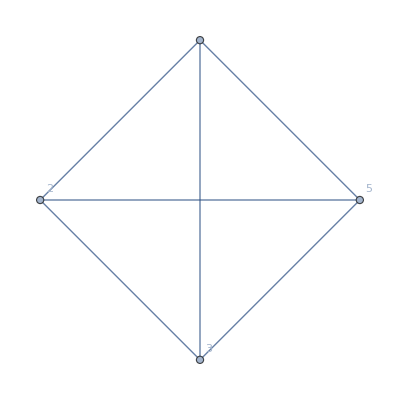

```mathematica
With[{e=UndirectedEdge[1,4]},{g4=EdgeDelete[g3,e],EdgeContract[g3,e]}]
```

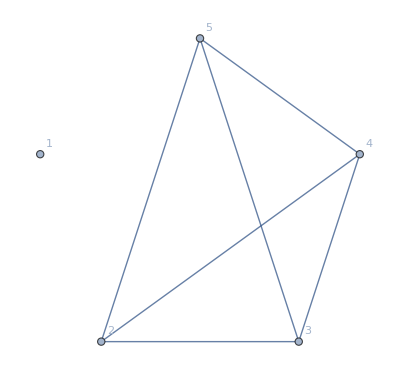
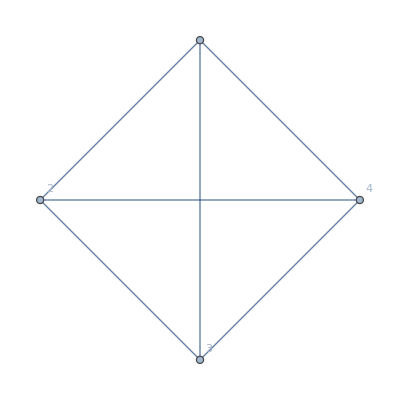

```mathematica
With[{e=UndirectedEdge[1,5]},{g5=EdgeDelete[g4,e],EdgeContract[g4,e]}]
```

```mathematica
GraphData["TriangleFree"]
```

{{4,2},{4,3},{5,2},{5,3},{5,4},{5,6},{5,7},{5,9},{5,14},{6,2},{6,3},{6,4},{6,5},{6,8},{6,9},3423,{ZeroTwoBipartite,{7,32}},{ZeroTwoBipartite,{7,33}},{ZeroTwoBipartite,{7,34}},{ZeroTwoBipartite,{7,35}},{ZeroTwoBipartite,{7,36}},{ZeroTwoBipartite,{7,37}},{ZeroTwoBipartite,{7,38}},{ZeroTwoBipartite,{7,39}},{ZeroTwoNonbipartite,{6,6}},{ZeroTwoNonbipartite,{6,9}},{ZeroTwoNonbipartite,{7,44}},{ZeroTwoNonbipartite,{7,45}},{ZeroTwoNonbipartite,{7,52}},{ZeroTwoNonbipartite,{7,53}}}
 |  |  |  |